# Mathematica Functions Lab #1

## Part I: How much space in the box?

Imagine you have a box.  It has height, width, and length, with variables as appropriate.  You wish to determine the volume (V) of this box, shown below in Figure 1.  The mathematical model for this is:

V = l × h × w

This is a simple equation to determine.  However, as a mathematical model, it’s wrong.  Why?  It’s wrong because there is actually some loss of volume because the walls of the box have some thickness, and that thickness takes up some of the volume of the box.  The improved mathematical model is:

V = (h-2t)×(w-2t)×(l-2t)

In this case, t is the thickness of the walls.  For all of the problems here, all of our measurements are in units of centimeters (cm).

-Graphics-
Figure 1:  Volume of a box | ()

### Lab Activity:

#### Build a model that determines the volume of a box that has a length of 200 cm, a width of 300 cm, and a height of 400 cm. The FUNCTION name should be: volumeNoWalls. Calculate the volume with these dimensions. REMEMBER that in Mathematica, you use a space to represent multiplication, not an “x” or a “*”. Your function should have THREE parameters. When you USE the function, make sure the answer has a variable name! For example: simpleVolume = volumeNoWalls[length, width, height].

```mathematica
volumeNoWalls[l_, w_, h_] := l w h
simpleVolume = volumeNoWalls[200, 300, 400];
Print["The volume is ", simpleVolume]
```

The volume is 24000000

#### Build a model that determines the volume of the box with the same dimensions but with a wall thickness of 5 cm. Calculate the volume with the same dimensions AND thickness = 5 cm. The FUNCTION name should be: volumeWithWalls. Your function should have FOUR parameters. When you USE the function, make sure you give this volume a variable name. For example, if the wall thickness was 5 cm, I would use something like “volume5cm”, for example: volume5cm = volumeWithWalls[...]

```mathematica
volumeWithWalls[l_, w_, h_, t_] := (l-2 t)  (w - 2 t)  (h-2 t)
volume5cm = volumeWithWalls[200, 300, 400, 5];
Print["The volume is ", volume5cm]
```

The volume is 21489000

#### Build a “comparison checker” (it’s the same formula as percent error). In this equation, you are determining by what percentage two values are different. The two sticks (“|”) are, if you don’t recognize them, the mathematical symbols for absolute value. REMEMBER that you never use ANY symbols for multiplication (x, *) -- you use a space! The “lower of the two values” means you find the MINIMUM of first value and second value.

percent difference = (| first value - second value |)/(lower of the two values) x 100

```mathematica
percentDifference[first_, second_] := N[Abs[first - second]/Min[first, second]] 100
```

#### Now, calculate the percent difference between the two volumes (the box with wall thicknesses that are “zero” (impossible!) and the box with a 5 cm thick wall).

```mathematica
difference = percentDifference[simpleVolume, volume5cm];
Print["The percent difference is ", difference, "%"]
```

The percent difference is 11.685%

#### What does your data suggest about the this assumption that the first box has walls with no thickness? Is is this a good assumption? If the percent difference is more than a small percentage -- like more than 5% -- then this is probably not a very good model.

TYPE YOUR ANSWER AFTER THIS LINE:  
The data suggest that the assumption is not a good one--the percent difference is quite high, at nearly 12%.

#### Calculate the volume of two boxes, one with a wall thickness of 5 cm and one with a thickness of 4 cm. Determine the percent difference. How do these two models compare?

```mathematica
volume5cm = volumeWithWalls[200, 300, 400, 5];
volume4cm = volumeWithWalls[200, 300, 400, 4];
difference = percentDifference[volume4cm, volume5cm];
Print["The percent difference is ", difference, "%"]
```

The percent difference is 2.27134%

TYPE YOUR ANSWER AFTER THIS LINE:
The two models are more similar; the percent difference is low, at about 2%.

#### Build a data table where you determine volumes for wall thicknesses going from 0 to 10 cm. Plot this data. Describe the graph.

```mathematica
myTable = Table[
{t,volumeWithWalls[200, 300, 400, t]},
{t, 0, 10}
];
Grid[myTable,Frame->All]
```

0 | 24000000
1 | 23483592
2 | 22974336
3 | 22472184
4 | 21977088
5 | 21489000
6 | 21007872
7 | 20533656
8 | 20066304
9 | 19605768
10 | 19152000

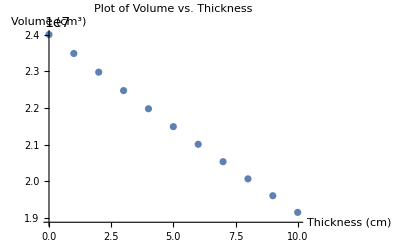

```mathematica
ListPlot[myTable, PlotLabel->"Plot of Volume vs. Thickness", AxesLabel->{"Thickness (cm)", "Volume (cm^3)"}]
```

The volume is decreasing linearly, as the thickness increases

#### Perform a linear regression of this dataset. What do you find as the value of the slope?

```mathematica
linearModel = LinearModelFit[myTable, x, x];
linearModel["BestFit"]
```

2.39475×10^7-484742. x

TYPE YOUR SLOPE ANSWER AFTER THIS LINE:
The slope is -484, 742

## Part II: The Logistic Model

### Description:

One of the more common models/algorithms found in computational science is the logistic function.  This model is primarily used to model population growth of an organism over some period of time.  The equation is:

ΔP = (P_0 M)/((M - P_0) e^(-r t) + P_0)

where P is the initial population (starting number of organisms), M is the carrying capacity (the maximum number of organisms that the environment can contain), r is the growth rate (provided as a percentage), and t is time.  
Notice that this is an exponential function, meaning that the results will typically have a curved shape when you plot them.

### Lab Activity:

#### Plot the logistic function with initial population P_0 = 20, carrying capacity M = 1000, and instantaneous rate of change of births r = 50% = 0.5 from t = 0 to t = 16 to obtain a graph.

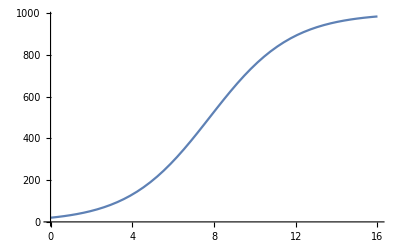

```mathematica
logisticFunc[p_, m_, r_, t_] := (p m)/((m - p) E^(-r t)+ p);
Plot[logisticFunc[20, 1000, 0.5,t ], {t, 0, 16}]
```

#### On the same graph in red, green, and blue, respectively, plot three logistic functions that each have M =1000 and r = 0.5 but P_0 values of 20, 100, and 200.

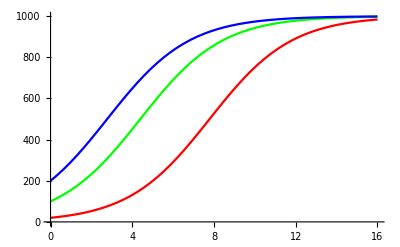

```mathematica
Plot[{logisticFunc[20, 1000, 0.5, t], logisticFunc[100, 1000, 0.5, t], logisticFunc[200, 1000, 0.5, t]}, {t, 0, 16}, PlotStyle->{Red, Green, Blue}]
```

#### What effect does P_0 have on a logistic graph?

TYPE YOUR ANSWER AFTER THIS LINE: 
It shifts the graph upwards/downwards

#### On the same graph, plot three logistic functions that each have M =1000 and P_0=20 but r values of 0.2, 0.5, and 0.8.

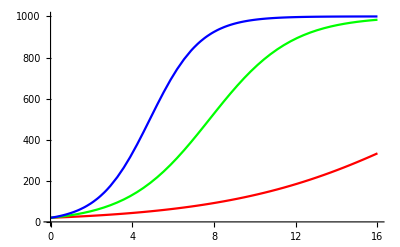

```mathematica
Plot[{logisticFunc[20, 1000, 0.2, t], logisticFunc[20, 1000, 0.5, t], logisticFunc[20, 1000, 0.8, t]}, {t, 0, 16}, PlotStyle->{Red, Green, Blue}]
```

#### What effect does r have on a logistic graph?

TYPE YOUR ANSWER AFTER THIS LINE: 
It affects the steepness of the curve

#### On the same graph in red, green, and blue, respectively, plot three logistic functions that each have P_0 = 20 and r = 0.5 but M values of 1000, 1300, and 2000.

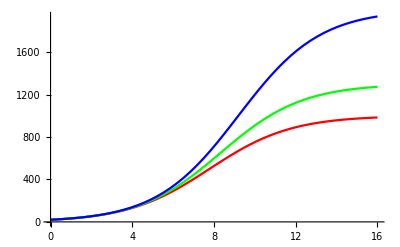

```mathematica
Plot[{logisticFunc[20, 1000, 0.5, t], logisticFunc[20, 1300, 0.5, t], logisticFunc[20, 2000, 0.5, t]}, {t, 0, 16}, PlotStyle->{Red, Green, Blue}]
```

#### What effect does M have on a logistic graph?

TYPE YOUR ANSWER AFTER THIS LINE:
It affects the maximum value (the carrying capacity) the graph approaches